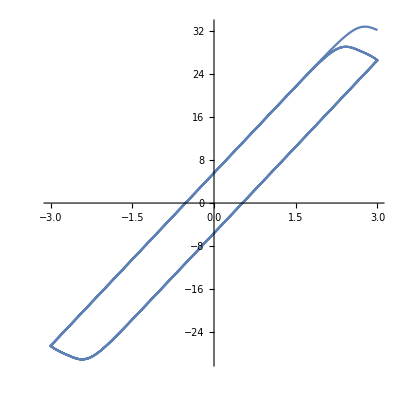

```mathematica
χ[t_]:=3Cos[t];
cycles=3;
α=5*RandomReal[];
κ=5*RandomReal[];
η=5*RandomReal[];
δ=5*RandomReal[];
ν=5*RandomReal[];
β=5*RandomReal[];
γ=5*RandomReal[];
n=5*RandomReal[];
s=NDSolve[{y'[t]==(δ*χ'[t]-ν*(β*Abs[χ'[t]]*Abs[y[t]]^(n-1)*y[t]+γ*χ'[t]*Abs[y[t]]^n))/η,y[0]==0},y,{t,0,cycles*2*π}];
f[t_]:=α*κ*χ[t]+(1-α)κ*η*Evaluate[y[t]/.Flatten@s]
ParametricPlot[{χ[t],f[t]},{t,0,cycles*2*π},AspectRatio->1]
```

```mathematica
Subscript[t, 0]=0;
Subscript[f, 0]=0;
steps=10000;
For[i=0,i<steps,i++,Subscript[f, i+1]=((δ*χ'[Subscript[t, i]]-ν*(β*Abs[χ'[Subscript[t, i]]]*Abs[Subscript[f, i]]^(n-1)*Subscript[f, i]+γ*χ'[Subscript[t, i]]*Abs[Subscript[f, i]]^n))/η)*(2*cycles*π)/steps+Subscript[f, i];Subscript[t, i+1]=Subscript[t, i]+2*cycles*π/steps];
fValues=Table[Subscript[f, i],{i,0,steps}];
Points=Table[{χ[Subscript[t, 0]+2*cycles*π*i/steps],α*κ*χ[Subscript[t, 0]+2*cycles*π*i/steps]+(1-α)κ*η*Subscript[f, i]},{i,0,steps}];
ListPlot[Points,AspectRatio->1];
```